Piecewise[{{((β-2 α) (Abs[r]-ϵ)^3)/ϵ^4+((2 β-3 α) (Abs[r]-ϵ)^2)/ϵ^3+(β (Abs[r]-ϵ))/ϵ^2-β/ϵ, r^2<ϵ^2}, {-β/Abs[r], True}}]

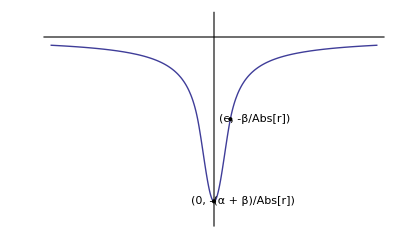

```mathematica
Clear[ inverseRadialSmoothedCap ] 

inverseRadialSmoothedCap[rr_, ee_, a_, b_] = 
Module[{vPlusCubic, vMinusCubic},
vPlusCubic[r_, e_, alpha_, beta_] =
Module[{vv, ww, s, v, aa, bb},
vv[r_] = aa ( r - e)^3/e^4 + bb(r - e)^2/ e^3 + beta(r - e)/e^2 - beta/e ;
ww[r_] = vv'[r] ;
s= Solve[ {-(beta + alpha)/e == vv[0], 0 == ww[0]}, {aa, bb}]  // Flatten ;

v[r_, e_, alpha_, beta_] = vv[r] /. s  ;

(*w[r_, e_, alpha_, beta_] = D[v[r, e, alpha, beta], r] ;
{v[e, e, α, β], w[e,e, α, β], v[0, e, α, β], w[0, e, α, β]} // Simplify*)

v[r, e, alpha, beta]
] ;

(*vMinusCubic[r_, e_, alpha_, beta_] =
Module[{vv, ww, s, v, aa, bb},
vv[r_] = aa ( r + e)^3/e^4 + bb(r + e)^2/ e^3 - beta(r + e)/e^2 - beta/e ;
ww[r_] = vv'[r] ;
s= Solve[ {-(beta + alpha)/e == vv[0], 0 == ww[0]}, {aa, bb}]  // Flatten ;

v[r_, e_, alpha_, beta_] = vv[r] /. s  ;

(*w[r_, e_, alpha_, beta_] = D[v[r, e, alpha, beta], r] ;
{v[e, e, α, β], w[e,e, α, β], v[0, e, α, β], w[0, e, α, β]} // Simplify*)

v[r, e, alpha, beta]
] ;

Piecewise[{{vPlusCubic[rr,ee,a,b],rr<ee&&rr>0},{vMinusCubic[rr,ee,a,b],rr>-ee&&rr<0}},-b/Abs[rr]]
*)

Piecewise[{{vPlusCubic[Abs[rr],ee,a,b],rr^2<ee^2}},-b/Abs[rr]]
] ;

inverseRadialSmoothedCap[r, ϵ, α, β] // TraditionalForm

Module[{e, a, b, range},
e = 0.5 ;
a = 1 ;
b = 1 ;
range = 5 ;
Plot[ 
{inverseRadialSmoothedCap[r, e, a, b](*, -1/r*)},
{r, -range, range}, 
PlotRange -> {Full, {-(a+b)/e-0.5, e}},
Ticks -> None,
(* http://mathematica.stackexchange.com/questions/13657/plot-showing-discontinuity-where-it-shouldnt *)
Exclusions->None,
Epilog->{
Point[ { e, -b/e} ],
Point[ { 0, -(b+a)/e} ],
Text["(ϵ, -β/Abs[r])", { 2.5 e, -b/e} ],
Text["(0, -(α + β)/Abs[r])", { 0.9, -(a + b)/e } ],
}
]
]

Clear[ inverseRadialSmoothedPeriodicExtension ]
inverseRadialSmoothedPeriodicExtension[r_, a_, e_, alpha_, beta_] =
Sum[ inverseRadialSmoothedCap[r + i a , e, alpha, beta], {i, -2, 2}] ;

Module[{a, e, alpha, beta, fourierTerms, sampleV},
a = 6 ;
e = 0.5 ; 
alpha = 1 ;
beta = 1 ;

sampleV[s_] = inverseRadialSmoothedPeriodicExtension[ s, a, e, alpha, beta] ;

fourierTerms[  nFourierTerms_ ] := 
Table[
 NIntegrate[ 
sampleV[ uu a]  Exp[- 2 Pi I( i uu )],
{uu, 0, 1}
(*,AccuracyGoal->5 *)
],
{i, 0, nFourierTerms}
] ;

fv = fourierTerms[ 25 ]  ;

fSeries[r_, n_] := fv[[1]] + 2 Re[ Sum[fv[[i+1]] Exp[ 2 Pi I i r /a], {i, 1, n}]]  ;
(*fSeries[r, 4]*)

(* Switched from Row to GraphicsRow: 
http://mathematica.stackexchange.com/questions/2058/sizing-cells-in-a-graphicsgrid-graphicsrow *)
Manipulate[
(*Graphics*)Row[{
Plot[ 
{sampleV[r],fSeries[r, n]},
{r, -20, 20},
PlotRange -> Full,
Exclusions->None,
PlotLegends->{ "v(r)", n }
],
Plot[ 
2 Re[ fv[[n+1]] Exp[ 2 Pi I n r /a] ],
{r, -20, 20},
PlotRange -> {Full, {-2, 2}},
Exclusions->None
]
}],
{{n, 1}, 1, 24, 1},
SaveDefinitions->True
]
]
```